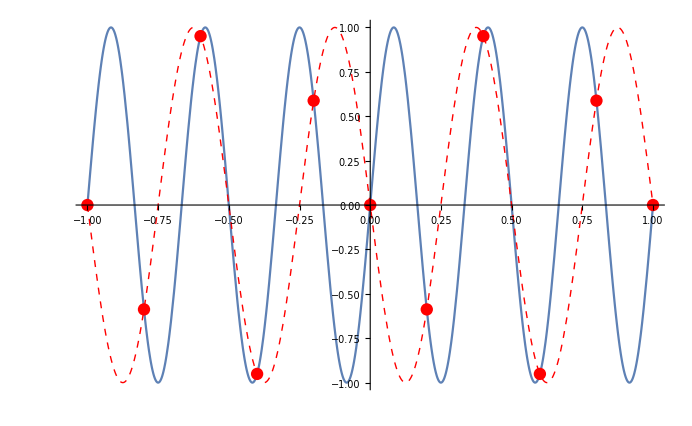

```mathematica
p1=Plot[Sin[6Pi t],{t,-1,1}];
p2=ListPlot[Transpose@{Range[-1,1,0.2],Sin[6 Pi#]&/@Range[-1,1,0.2]},PlotStyle->Red];
p3=Plot[-Sin[4Pi t],{t,-1,1},PlotStyle->{Dashed,Red,Thick}];
Show[p1,p2,p3]
```